## First Plot

```mathematica
SetDirectory[NotebookDirectory[]];
dataRaw=Import["modelFit.csv"];
labels=dataRaw[[1,3;;All]]
data=dataRaw[[2;;All,3;;All]]
```

{A_M_Pred,A_Av_M_Obs,A_F_Pred,A_Av_F_Obs,B_M_Pred,B_Av_M_Obs,B_F_Pred,B_Av_F_Obs,C_M_Pred,C_Av_M_Obs,C_F_Pred,C_Av_F_Obs,D_M_Pred,D_Av_M_Obs,D_F_Pred,D_Av_F_Obs}

{{0.047619,0.047619,0,0,0.2,0.2,0,0,0.333333,0.333333,0,0,0.5,0.5,0,0},{0.086,0.08476,0,0.00025,0.315333,0.270208,0,0.00152934,0.473,0.401054,0,0.00367502,0.946,0.549596,0,0.0166616},{0.08132,0.122258,0.0000360494,0.00102083,0.297658,0.31739,0.000647006,0.00394758,0.445567,0.435863,0.0018913,0.0126913,0.821085,0.569134,0.0738306,0.0309902},{0.076834,0.15229,0.0000675945,0.0034745,0.279815,0.327272,0.00129495,0.0144152,0.416118,0.424509,0.00404437,0.027417,0.610408,0.451269,0.147409,0.0544324},{0.0725425,0.197691,0.0000948074,0.00727579,0.262111,0.334421,0.00191787,0.0211839,0.385964,0.367229,0.00631112,0.038692,0.49903,0.384477,0.169296,0.0706009},{0.0684431,0.214025,0.000117984,0.0104468,0.244687,0.314694,0.00249915,0.0309273,0.355613,0.331076,0.00856435,0.0399378,0.407921,0.442187,0.175854,0.0820593},{0.064533,0.181537,0.000137429,0.0200168,0.227691,0.285798,0.00302505,0.0373203,0.325734,0.296654,0.0106815,0.0418002,0.340718,0.434656,0.171659,0.130763},{0.0608084,0.2112,0.000153452,0.0221861,0.21126,0.333349,0.00348536,0.0450509,0.296907,0.303426,0.0125641,0.0658841,0.289592,0.481508,0.16324,0.189022},{0.0572654,0.217405,0.000166361,0.0376065,0.195506,0.340555,0.00387376,0.0623628,0.2696,0.376694,0.0141472,0.103353,0.250173,0.477475,0.1533,0.156916}}

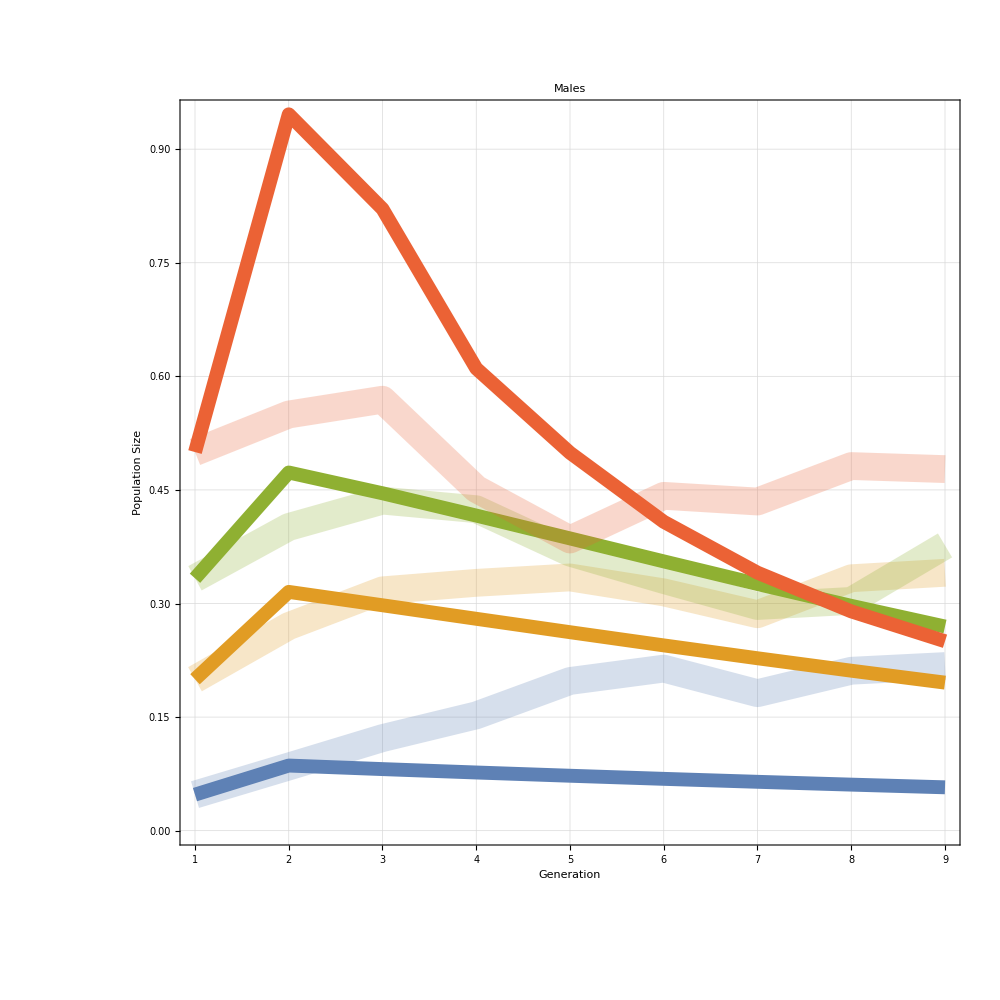
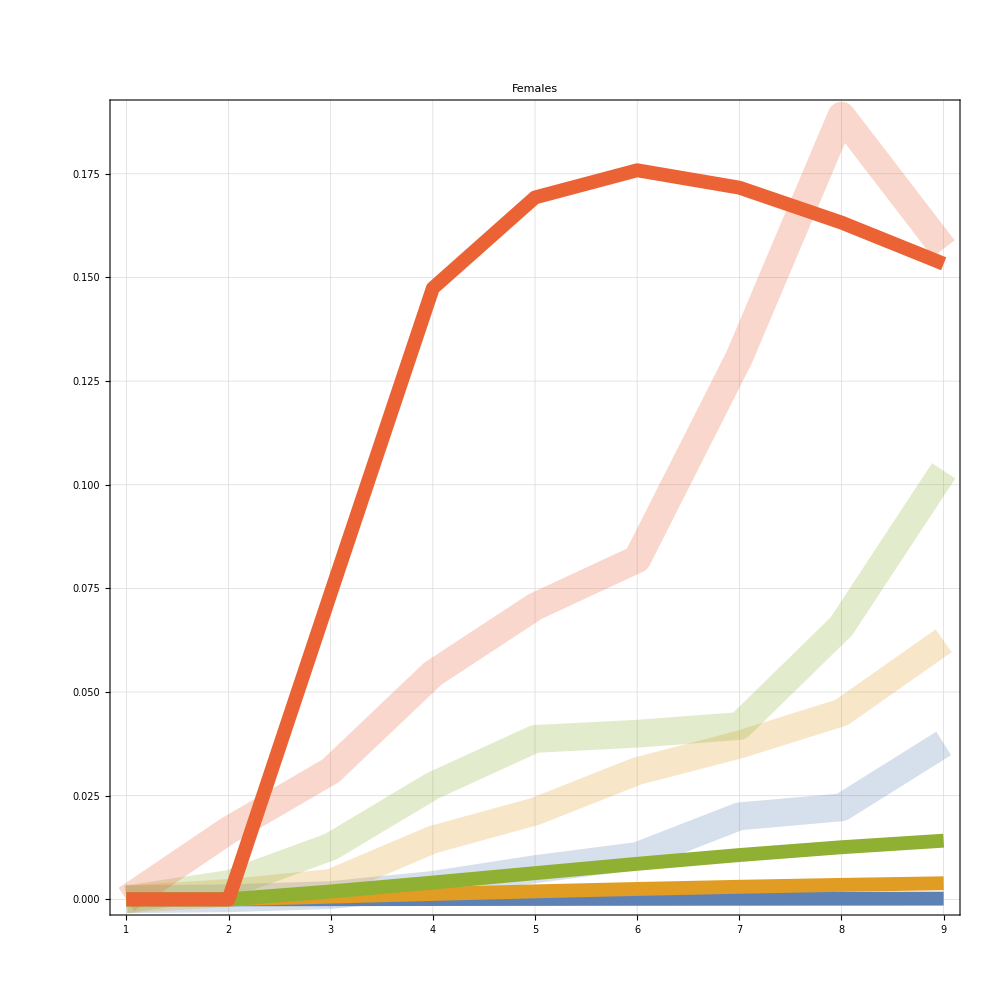
-Graphics- | -Graphics- |

experimentsGrid.pdf

```mathematica
plotOneIndices=Flatten[Position[labels,#]&/@{"A_M_Pred","A_Av_M_Obs","B_M_Pred","B_Av_M_Obs","C_M_Pred","C_Av_M_Obs","D_M_Pred","D_Av_M_Obs"}];
selected=Transpose[data][[plotOneIndices]];
males=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Thickness[.01],#],Directive[Opacity[.25],Thickness[.02],#]}&/@ColorData[97,"ColorList"][[1;;(plotOneIndices//Length)]]//Flatten)),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"Generation","Population Size"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Males",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
plotOneIndices=Flatten[Position[labels,#]&/@{"A_F_Pred","A_Av_F_Obs","B_F_Pred","B_Av_F_Obs","C_F_Pred","C_Av_F_Obs","D_F_Pred","D_Av_F_Obs"}];
selected=Transpose[data][[plotOneIndices]];
females=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Thickness[.01],#],Directive[Opacity[.25],Thickness[.02],#]}&/@ColorData[97,"ColorList"][[1;;(plotOneIndices//Length)]]//Flatten)),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"",""}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Females",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;4]],{"1","2","3","4"},
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["Experiment",30]
];
grid=Grid[{{males,females,swatch}}]
Export["experimentsGrid.pdf",grid]
```

## Second Plot

```mathematica
SetDirectory[NotebookDirectory[]];
dataRaw=Import["modelFit2.csv"];
labels=dataRaw[[1,3;;All]]
data=dataRaw[[2;;All,3;;All]];
```

{D_Female_Pred,D_D_Allele_Pred,D_W_Allele_Pred,D_R_Allele_Pred,D_B_Allele_Pred,I_Female_Pred,I_D_Allele_Pred,I_W_Allele_Pred,I_R_Allele_Pred,I_B_Allele_Pred}

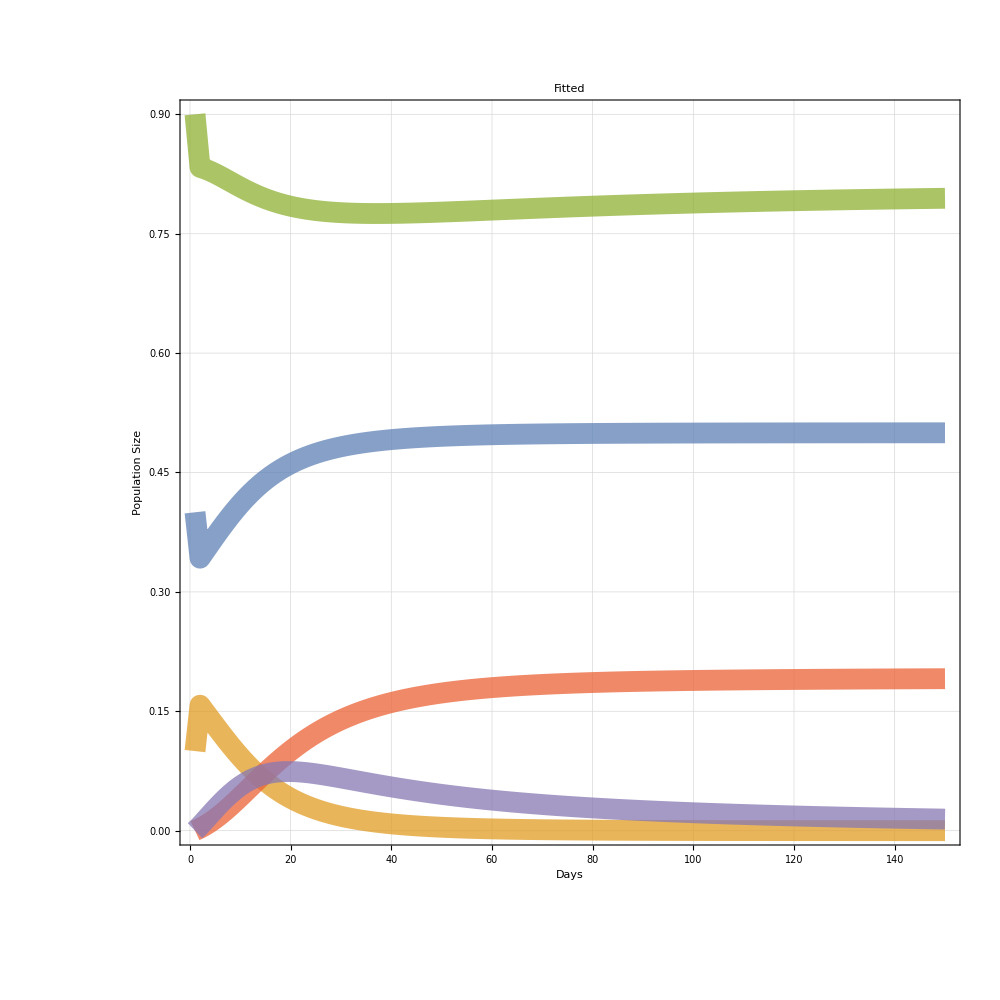
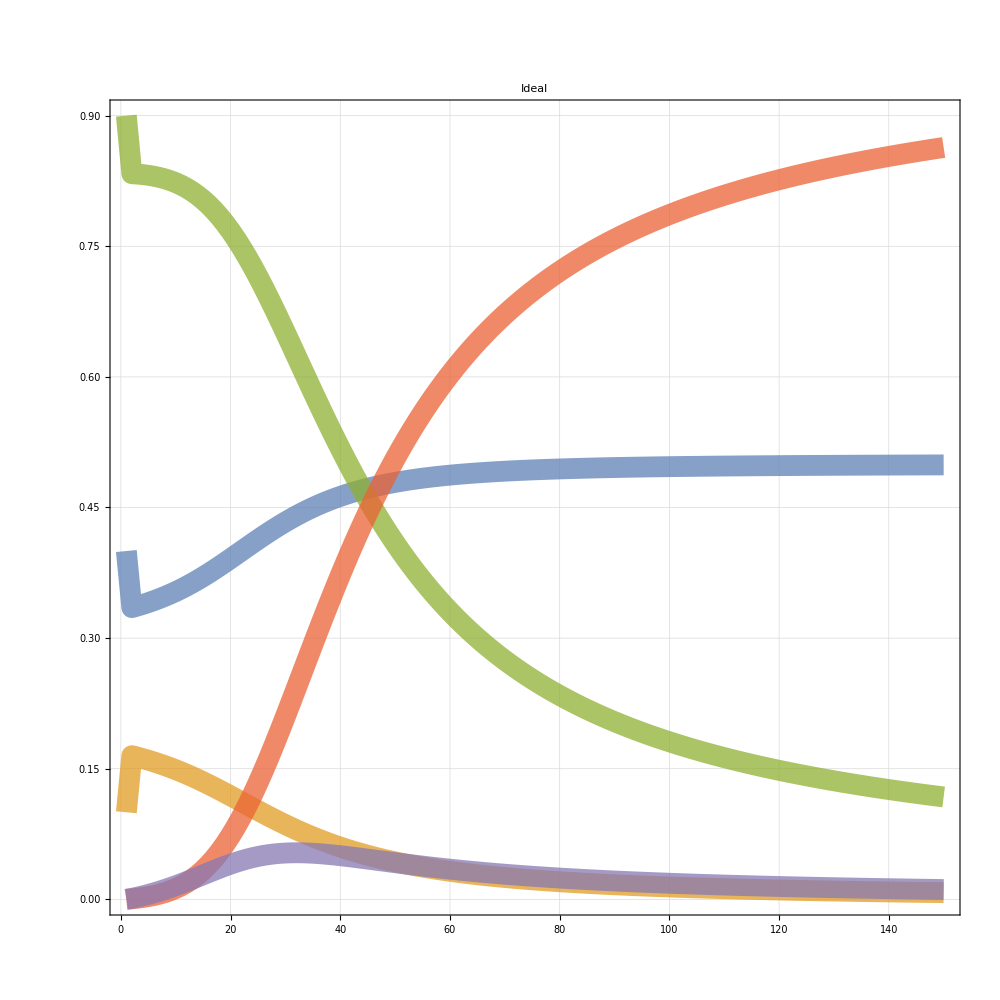
-Graphics- | -Graphics- |

experimentsGrid2.pdf

```mathematica
plotOneIndices=Flatten[Position[labels,#]&/@{"D_Female_Pred","D_D_Allele_Pred","D_W_Allele_Pred","D_R_Allele_Pred","D_B_Allele_Pred"}];
selected=Transpose[data][[plotOneIndices]];
males=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[plotOneIndices]]])),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"Days","Population Size"}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Fitted",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
plotOneIndices=Flatten[Position[labels,#]&/@{"I_Female_Pred","I_D_Allele_Pred","I_W_Allele_Pred","I_R_Allele_Pred","I_B_Allele_Pred"}];
selected=Transpose[data][[plotOneIndices]];
females=ListLinePlot[selected,
PlotStyle->({#}&/@({Directive[Opacity[.75],Thickness[.015],#]}&/@ColorData[97,"ColorList"][[1;;Length[plotOneIndices]]])),
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Gray,Thickness[.0075]],
BaseStyle->20,
FrameLabel->(Style[#,Gray,30]&/@{"",""}),
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[.0001],Opacity[.5]],
PlotLabel->Style["Ideal",Gray,40],
ImageSize->1000,
PlotRange->{{1,All},All}
];
swatch=SwatchLegend[ColorData[97,"ColorList"][[1;;5]],{"B","D","XX","R","W"},
LegendMarkerSize->30,
LabelStyle->Directive[Gray,25],
LegendLabel->Style["Experiment",30]
];
grid=Grid[{{males,females,swatch}}]
Export["experimentsGrid2.pdf",grid]
```